```mathematica
(* Set directory is required for each cold start. Modify this to your dir. *)
SetDirectory["/Users/plumbus/Projects/astro"];
```

```mathematica
areaFiles = FileNames["./bench/run/area-*.json"];
areaJSON = Import[#1]&/@areaFiles;
areaJSONValues = Transpose@Values@areaJSON;
```

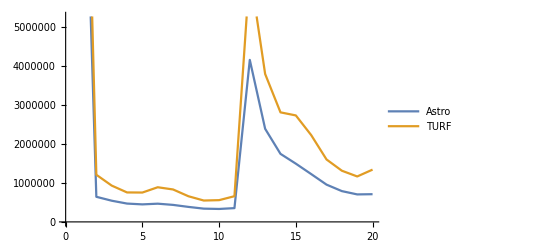

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
ListLinePlot[areaJSONValues, PlotLegends->{"Astro", "TURF"}]
```

```mathematica
astroMean = Mean[areaJSONValues[[1]]]
turfMean = Mean[areaJSONValues[[2]]]
```

Mean[Values[areaFiles]]

Part::partw: Part 2 of Transpose[Values[areaFiles]] does not exist.

Mean[Transpose[Values[areaFiles]]⟦2⟧]

```mathematica
unionFiles = FileNames["./bench/run/union-*.json"];
unionJSON = Import[#1]&/@unionFiles;
unionJSONValues = Transpose@Values@unionJSON;
```

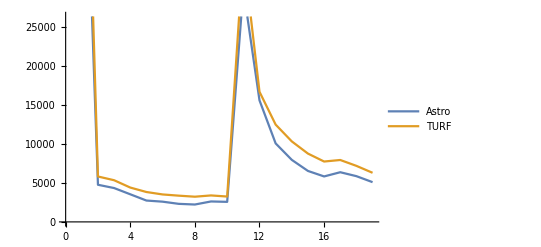

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
ListLinePlot[unionJSONValues, PlotLegends->{"Astro", "TURF"}]
```

```mathematica
unionAstroMean = Mean[unionJSONValues[[1]]]
unionTurfMean = Mean[unionJSONValues[[2]]]
```

9190.71

11510.9

```mathematica
intersectFiles = FileNames["./bench/run/intersect-*.json"];
intersectJSON = Import[#1]&/@intersectFiles;
intersectJSONValues = Transpose@Values@intersectJSON;
```

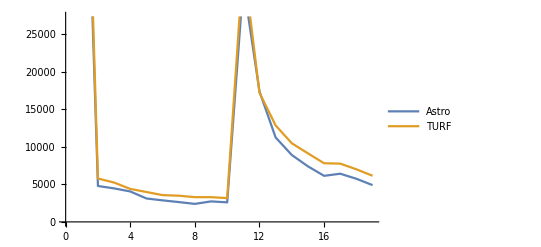

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
ListLinePlot[intersectJSONValues, PlotLegends->{"Astro", "TURF"}]
```

```mathematica
intersectAstroMean = Mean[intersectJSONValues[[1]]]
intersectTurfMean = Mean[intersectJSONValues[[2]]]
```

10549.3

11878.1